```mathematica
Quit[];
```

# pk EFT + IR resummations

Alejandro Aviles
avilescervantes@gmail.co

## ini

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/waco/Desktop/sMGPT

```mathematica
FileIniNW="./code_NW/outputs/F4z05_NW/FullMG/AllFunctions_F4z05_NW_FullMG.dat"
FileIni="./code/outputs/F4z05/FullMG/AllFunctions_F4z05_FullMG.dat"
```

./code_NW/outputs/F4z05_NW/FullMG/AllFunctions_F4z05_NW_FullMG.dat

./code/outputs/F4z05/FullMG/AllFunctions_F4z05_FullMG.dat

## Import theory

```mathematica
<<readtheory.m
```

f(k=0) = 0.733327

test Ploop(k=0.2,mu=0.8)=966.688

f(k=0) = 0.733327

test PloopNW(k=0.2,mu=0.8)=1145.22

```mathematica
pk[k_,mu_,b1_,b2_,bs2_,b3nl_,alpha0_,alpha2_,alpha4_,ctilde_,alphashot0_,alphashot2_,PshotP_]:=(b1+fk[k] mu^2)^2(PSLNW[k]+Exp[-k^2 Sigma2Total[mu]] (PSL[k]-PSLNW[k]) (1+k^2 Sigma2Total[mu]))+Exp[-k^2 Sigma2Total[mu]] Ploop[k,mu,b1,b2,bs2,b3nl,alpha0,alpha2,alpha4,ctilde,alphashot0,alphashot2,PshotP]+(1-Exp[-k^2 Sigma2Total[mu]]) PloopNW[k,mu,b1,b2,bs2,b3nl,alpha0,alpha2,alpha4,ctilde,alphashot0,alphashot2,PshotP];


pk[0.2,1,1.2,0.2,0.01,0.001,0.2,0.2,1,1.2,0.2,0.01,0.001]
DNLOell0[0.2,2];
```

11226.1

## IR-resummed power spectrum

```mathematica
k=0.1;
mu=0;
b1=1.44;
b2=-1;
bs2=-4/7(b1-1); 
b3nl=32/315(b1-1);
alpha0=-10;  (*EFT param ell=0*)
alpha2=-44; (*EFT param ell=2*)
alpha4=-2.9; (*EFT param ell=4*)
ctilde=-0.38; (*EFT param NLO*)

alphashot2=0; (*This is the non constant noise. Use either this one, or ctilde *)
PshotP=1/0.000208;  (*This is the Poissonian shot noise *)
alphashot0=1; (*The constant noise is Poisson*alphashot0 is the Poissonian shot noise. Hence, alphashot0 and PshotP are degenerate*)

pkIR[k_,mu_]:=pk[k,mu,b1,b2,bs2,b3nl,alpha0,alpha2,alpha4,ctilde,alphashot0,alphashot2,PshotP];
pkIR[k,mu]
```

11891.3

## Multipoles

```mathematica
(*np=1;*)
Needs["NumericalDifferentialEquationAnalysis`"] (*This is for GL angular integration*)
Nx=16;
tGL=GaussianQuadratureWeights[Nx,-1,1];
xGL=Table[tGL[[ii,1]],{ii,1,Nx}];
wGL=Table[tGL[[ii,2]],{ii,1,Nx}];
```

```mathematica
pkell0T={};
Do[
kp=kT[[i]];
monp=0;
Do[
muv=xGL[[xii]];
w=wGL[[xii]];
PMEev=pkIR[kp,muv];
monp=monp+w*PMEev/2;
,{xii,1,Nx}];
AppendTo[pkell0T,{kp,monp}]
,{i,1,Length@kT}];


pkell2T={};
Do[
kp=kT[[i]];
quadp=0;
Do[
muv=xGL[[xii]];
w=wGL[[xii]];
PMEev=pkIR[kp,muv];
quadp=quadp+w*PMEev*LegendreP[2,muv]5./2.;
,{xii,1,Nx}];
AppendTo[pkell2T,{kp,quadp}]
,{i,1,Length@kT}];

pkell4T={};
Do[
kp=kT[[i]];
hexap=0;
Do[
muv=xGL[[xii]];
w=wGL[[xii]];
PMEev=pkIR[kp,muv];
hexap=hexap+w*PMEev*LegendreP[4,muv]9./2.;
,{xii,1,Nx}];
AppendTo[pkell4T,{kp,hexap}]
,{i,1,Length@kT}];
```

## Export

```mathematica
header="# 1.k[h/Mpc]   2.Pell0   3.Pell2  4.Pell4";
exportT=Table[{kT[[i]],pkell0T[[i,2]],pkell2T[[i,2]],pkell4T[[i,2]]},{i,1,Length@kT}];
PrependTo[exportT,header];
Export["multipoles.dat",exportT]
```

multipoles.dat

## Plots

```mathematica
pkell0=Interpolation[pkell0T]
pkell2=Interpolation[pkell2T];
pkell4=Interpolation[pkell4T];
```

InterpolatingFunction[{{0.001, 1.}}, <>]

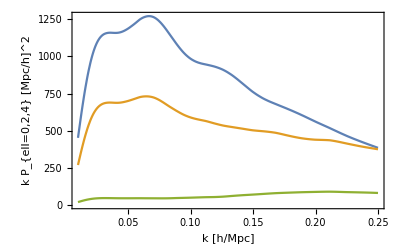

```mathematica
pellgr=Plot[{k (pkell0[k]-PshotP*alphashot0),k pkell2[k],k pkell4[k]},{k,0.01,0.25},Frame->True,ImageSize->400,FrameLabel->{"k [h/Mpc]","k P_{ell=0,2,4}  [Mpc/h]^2"}]
```